# Record breaking statistic

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","DJI_NASDAQ_MXX_NIKKEI_dataset.wdx"}];
(*path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];*)
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};
```

Date fixer: There are no dates in the original dataset, this generates the intermediate dates.

```mathematica
GenerateDaysBetween[firstDate_DateObject,lastDate_DateObject,length_]:=Block[{dayRange,dayCount,ratio},
dayRange = DayRange[firstDate,lastDate];
dayCount = DayCount[firstDate,lastDate];
ratio = dayCount/length;
Table[Part[dayRange,Floor[i*ratio]],{i,length}]
];
AddToDataset[database,"Dates",GenerateDaysBetween[DateObject[#1],DateObject[#2],Length[#3]]&,{"FirstDate","LastDate","Prices"}];
```

Important dates

```mathematica
rules = {"Black Monday"->"(a)","Japanese asset\nprice bubble"-> "(b)","Tequila effect"->"(c)","Dotcom bubble"->"(d)","Subprime crisis"->"(e)","Brexit"->"(f)"};
dateNames = {"Black Monday","Japanese asset\nprice bubble","Tequila effect","Dotcom bubble","Subprime crisis","Brexit"}/.rules;
dateObjects = {DateObject[{1987,10,19},"Day","Gregorian",-6.],DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]};

AddKeyToMarket[database[[1]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[1]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[2]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[2]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[3]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[3]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[4]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[4]],"ImportantDates"->dateObjects];

orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Samples size

```mathematica
GetInfo[market_]:=Module[{name,sampleSize,partitionSize,firstDate, lastDate},
name = market["Name"];
sampleSize = Length[market["Prices"]];
partitionSize = Length[Partition[TrendDuration[market["Prices"]],500,1]];
firstDate = DateString[market["FirstDate"],"ISODate"];
lastDate = DateString[market["LastDate"],"ISODate"];

Return[{name,sampleSize,partitionSize, firstDate,lastDate}];
];
```

```mathematica
info = Map[GetInfo,database];
Grid[Join[{{"Market name","Sample size","Partition size","First date","Last date"}},info],Background->{None,{Gray}}]
```

Market name | Sample size | Partition size | First date | Last date
DJIA | 9932 | 4630 | 1978-10-30 | 2018-01-23
NASDAQ Composite | 9895 | 4003 | 1978-10-30 | 2018-01-23
IPC | 9795 | 3716 | 1978-10-30 | 2018-01-23
Nikkei 225 | 9682 | 4349 | 1978-10-30 | 2018-01-23

## Record statistic for trend duration

```mathematica
NewRecord[lastRecord_,list_]:=SelectFirst[list,#>lastRecord&];
GetRecords[list_]:=Block[{recordCanditates,records},
recordCanditates = DeleteDuplicates[list];
records = DeleteCases[Drop[FixedPointList[NewRecord[#,recordCanditates]&,0],1],_Missing];
Return[records];
];
Diff[prices_, lag_:1]:= If[Length[prices]≥ 2,
Drop[prices, lag] - Drop[prices, -lag],
Nothing
];
GetRecordTimes[list_]:=Diff[Flatten[Map[FirstPosition[list,#]&,GetRecords[list]]]];
GetWindowedRecordTimes[list_,window_]:=Flatten[Map[GetRecordTimes,Partition[list,UpTo[window]]]];
GetWindowedRecordTimes[list_,window_,skip_]:=Flatten[Map[GetRecordTimes,Partition[list,UpTo[window],skip]]];
GetNumberOfRecordBreaks[list_,window_,skip_]:=Map[Length[GetRecordTimes[#]]&,Partition[list,UpTo[window],skip]];
```

```mathematica
records = Map[GetRecordTimes[TrendDuration[#["Prices"]]]&,database]
```

{{4,5,12,105,218,687},{4,1,2,2,50,14},{6,3,261},{1,4,10,1052,3750}}

```mathematica
ListLinePlot[records,
PlotRange->All,
PlotLegends->Placed[LineLegend[orderedDatabase[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Time",15], Style["Record value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"Records",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}},
Frame->True
]
```

```mathematica
HistogramPoints[data_]:=Map[{#,Count[data,#]}&,Sort[DeleteDuplicates[data]]];
HistogramPoints[data_,bspec_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Count"],1]];
HistogramPointPlot[data_List,opts: OptionsPattern[]]:=Block[{pltData = Map[HistogramPoints,data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->Take[Map[{#,{PointSize[Large],#}}&,colors],Length[data]],
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
RecordTimesStatistic[market_,window_]:=Block[{prices = market["Prices"],part,result},
part = Partition[TrendDuration[prices],UpTo[window],1];
result = Flatten[Map[GetRecordTimes,part]];
Return[result];
];
RecordTimesStatisticPlot[market_,window_,scaling_ :None]:=Block[{prices = market["Prices"],fittedDist,fittedPts,data,pltData,p,model,a,k,t,fit,fittedModel},
data = RecordTimesStatistic[market,window];
pltData = HistogramPoints[data];

(*model= k t^a;
fit = FindFit[pltData,model,{a,k},t];
fittedModel = model /.FindFit[pltData,model,{a,k},t];

fittedPts = Table[{t,fittedModel},{t,Min[data],Max[data],1}];*)


ListPlot[
pltData,
Joined->{False,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["Count",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->scaling
]
];
```

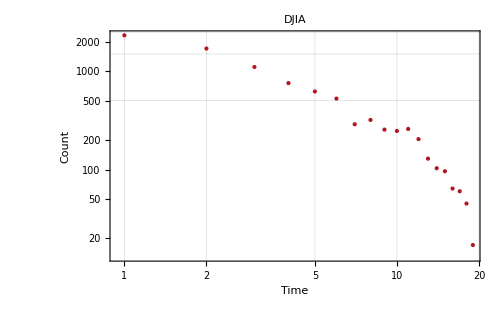
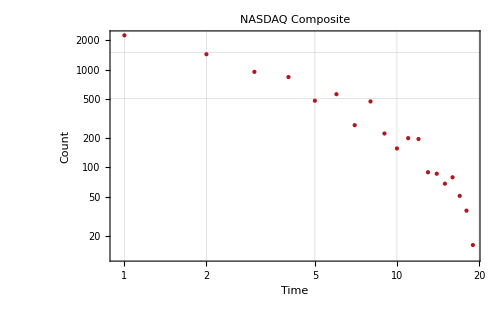
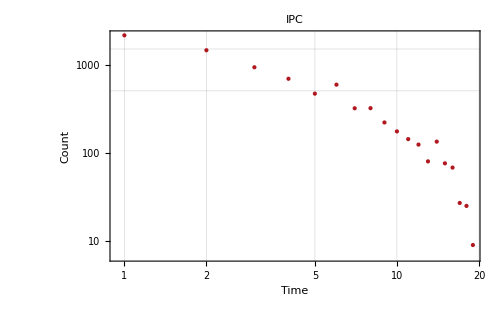
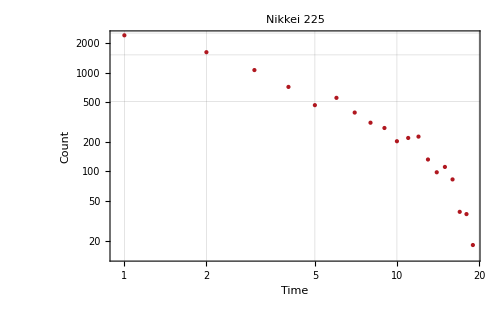

```mathematica
Map[RecordTimesStatisticPlot[#,20,{"Log","Log"}]&,database]
```

```mathematica
Map[Export[StringJoin[{NotebookDirectory[],"/",#["Name"],"_trendDuration.csv"}],HistogramPoints[RecordTimesStatistic[#,20]]]&,database]
```

{/home/carlos/Documentos/Programacion/EconomicComputations/Applications//DJIA_trendDuration.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//NASDAQ Composite_trendDuration.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//IPC_trendDuration.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//Nikkei 225_trendDuration.csv}

### Number of record breaks

```mathematica
NumberOfRecordBreaksHistogram[market_,window_,skip_]:=Block[{recordBreaks},
recordBreaks = GetNumberOfRecordBreaks[TrendDuration[market["Prices"]],window,skip];
Histogram[
recordBreaks,
Automatic,
"Probability",
PlotTheme->"Monochrome", 
FrameLabel->{Style["Number of record breaks",15], Style["Probability",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
Frame->True
]
];
```

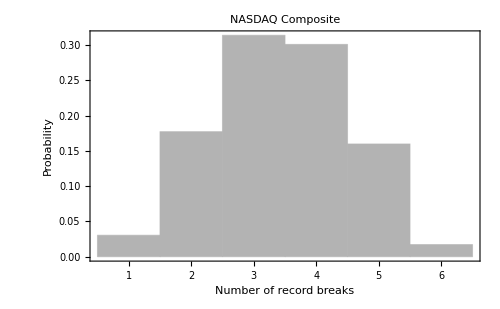
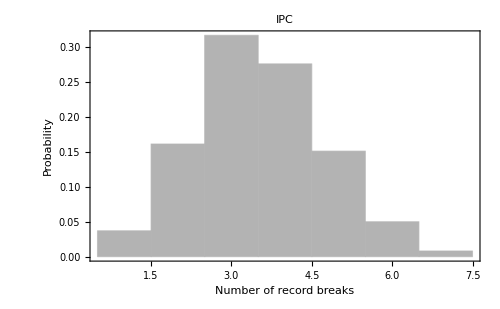
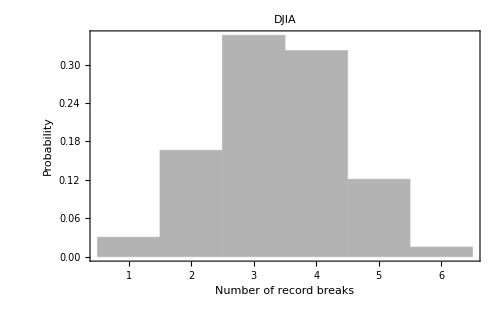
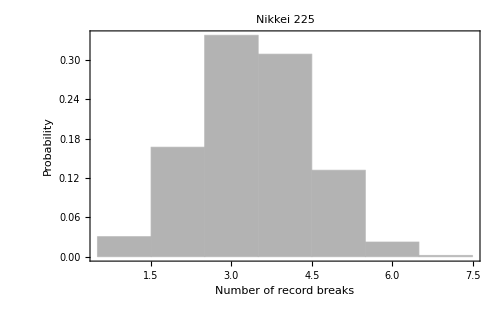

```mathematica
Map[NumberOfRecordBreaksHistogram[#,50,1]&,orderedDatabase]
```

```mathematica
DatedTrendDuration[datedPrices_]:=Block[{endpoints,datedTD},
endpoints = Map[First, TakeList[datedPrices, Append[TrendDuration[datedPrices[[All, 2]]], All]]];
datedTD = Transpose[{Drop[endpoints[[All, 1]],-1], TrendDuration[datedPrices[[All, 2]]]}];
Return[datedTD];
];
DatedPrices[market_]:=Thread[{market["Dates"],market["Prices"]}];
DatedNumberOfRecordBreaks[datedPrices_List, window_ :50, skip_ :1]:=Block[{dtd},
dtd = DatedTrendDuration[datedPrices];
Thread[{dtd[[All,1]],GetNumberOfRecordBreaks[dtd[[All,2]],window,skip]}]
];
DatedNumberOfRecordBreaks[market_Association, window_ :50, skip_ :1]:=Block[{datedPrices,dtd},
datedPrices = DatedPrices[market];
dtd = DatedTrendDuration[datedPrices];
Thread[{dtd[[All,1]],GetNumberOfRecordBreaks[dtd[[All,2]],window,skip]}]
];
DatedNumberOfRecordBreaksPlot[market_, window_ :50, skip_ :1]:=DateListPlot[
DatedNumberOfRecordBreaks[market, window, skip],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Record Breaks",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
InterpolationOrder->0
];
```

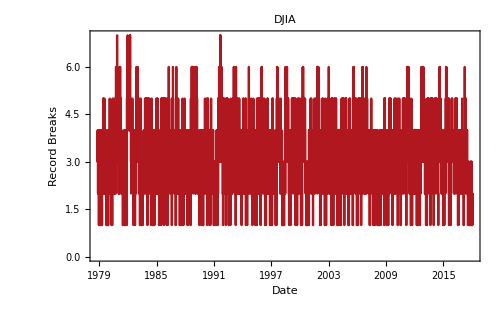
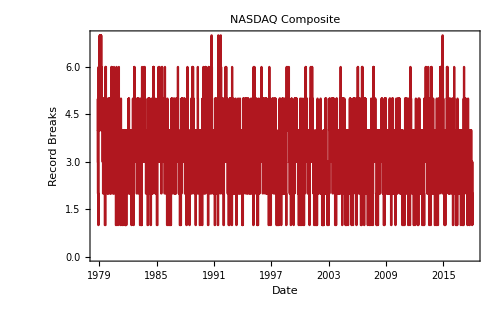
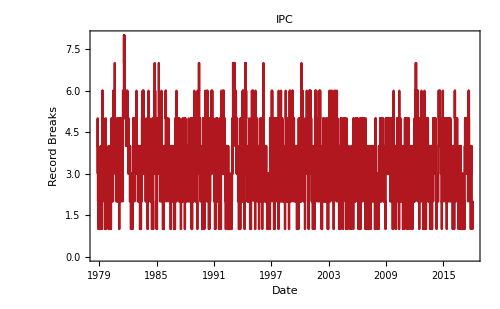
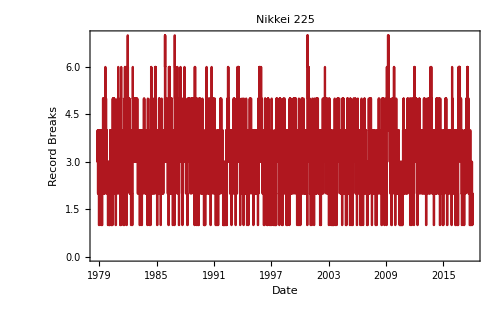

```mathematica
Map[DatedNumberOfRecordBreaksPlot,database]
```

## Record breaking statistics for returns

```mathematica
RecordTimesStatistic[market_,observableFunction_,window_]:=Block[{prices = market["Prices"],part,result},
part = Partition[observableFunction[prices],UpTo[window],1];
result = Flatten[Map[GetRecordTimes,part]];
Return[result];
];
RecordTimesStatisticPlot[market_,observableFunction_,window_,scaling_ :None]:=Block[{prices = market["Prices"],fittedDist,fittedPts,data,pltData,p,model,a,k,t,fit,fittedModel},
data = RecordTimesStatistic[market,observableFunction,window];
pltData = HistogramPoints[data];
model= k t^a;
fit = FindFit[pltData,model,{a,k},t];
fittedModel = model /.FindFit[pltData,model,{a,k},t];

fittedPts = Table[{t,fittedModel},{t,Min[data],Max[data],1}];


ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["Count",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->scaling,
PlotLegends->Placed[LineLegend[{"Data",Row[{"Fit: ",StandardForm[fittedModel]}]},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
]
];
```

### Returns

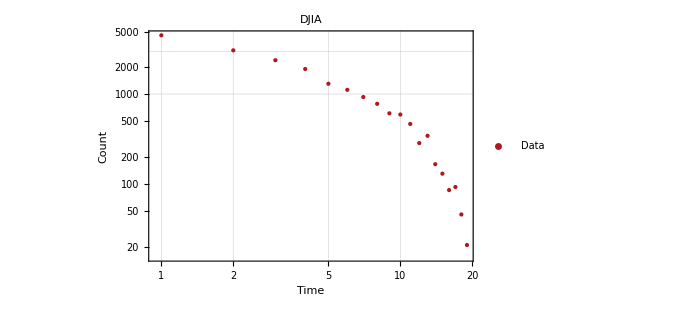
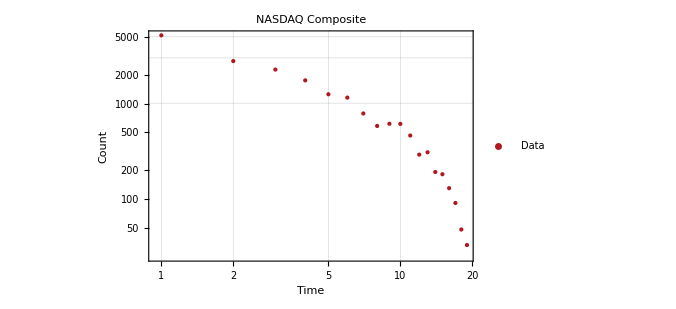
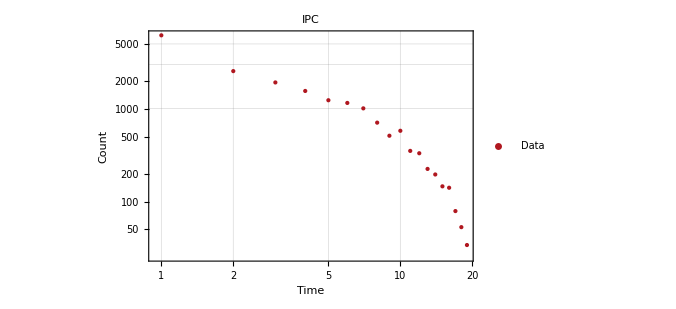
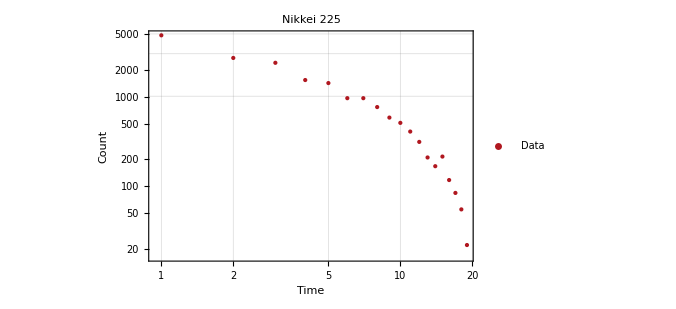

```mathematica
Map[RecordTimesStatisticPlot[#,Returns,20,{"Log","Log"}]&,database]
```

```mathematica
Map[Export[StringJoin[{NotebookDirectory[],"/",#["Name"],"_returns.csv"}],HistogramPoints[RecordTimesStatistic[#,Returns,20]]]&,database]
```

{/home/carlos/Documentos/Programacion/EconomicComputations/Applications//DJIA_returns.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//NASDAQ Composite_returns.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//IPC_returns.csv,/home/carlos/Documentos/Programacion/EconomicComputations/Applications//Nikkei 225_returns.csv}

### Trend returns

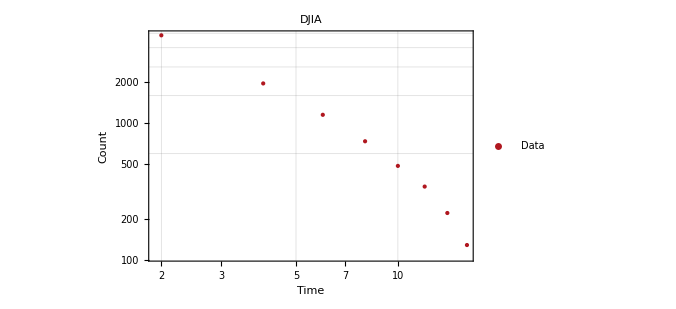
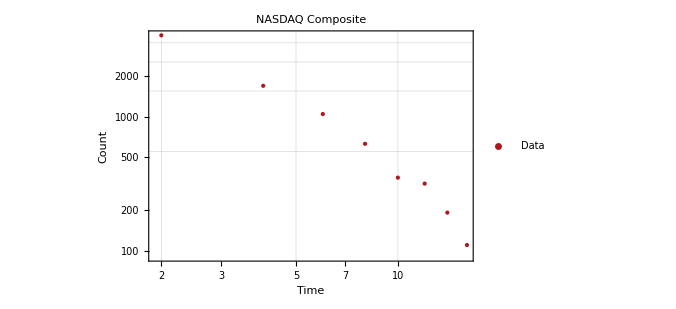
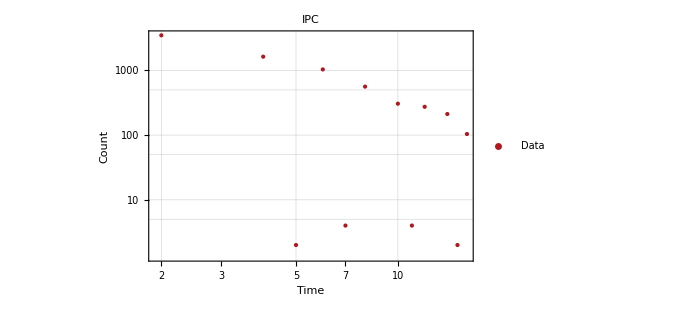
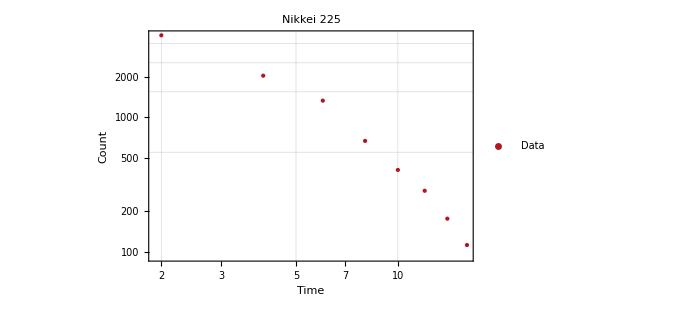

```mathematica
Map[RecordTimesStatisticPlot[#,TrendReturns,20,{"Log","Log"}]&,database]
```

# Ideas to fix my fuckup

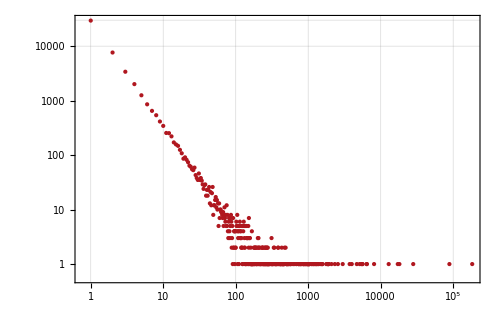

```mathematica
HistogramPointPlot[RandomVariate[ZipfDistribution[0.95],50000],ScalingFunctions->{"Log","Log"}]
```

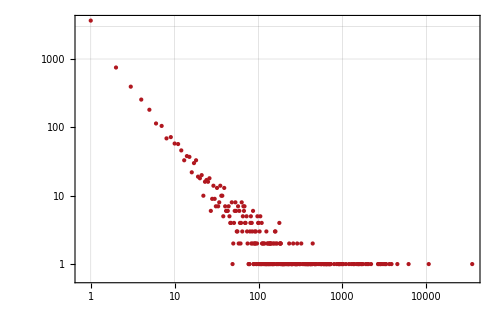

```mathematica
HistogramPointPlot[
Flatten[Table[Diff[Sort[RandomVariate[ZipfDistribution[0.95],100]]],500]],
ScalingFunctions->{"Log","Log"}
]
```

In this experiment I generate 50000 pseudorandom numbers with a power-law distribution defined as

```mathematica
PDF[ZipfDistribution[0.95],l]
```

Piecewise[{{0.590169/l^1.95, l≥1}, {0, True}}]

A sorted number sequence with this distribution, defined as l, is analogous to the wrongly calculated record breaking waiting time that it was actually a plain  record breaking time.

An exampe of 50 sorted pseudorandom numbers generated with a power-law distribution.

```mathematica
Sort[RandomVariate[ZipfDistribution[0.95],50]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,3,3,4,5,5,6,9,14,20,25,26}

It is possible to obtain the record breaking waiting time sequence k from the record breaking time sequence l by taking the differences between record breaking times.

```mathematica
Diff[seq_, lag_:1]:= Drop[seq, lag] - Drop[seq, -lag];
```

```mathematica
Diff[Sort[RandomVariate[ZipfDistribution[0.95],50]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,3,2,18,15}

For the k distribution, 10000 sequences of 200 transformed points were generated. The results are shown below.

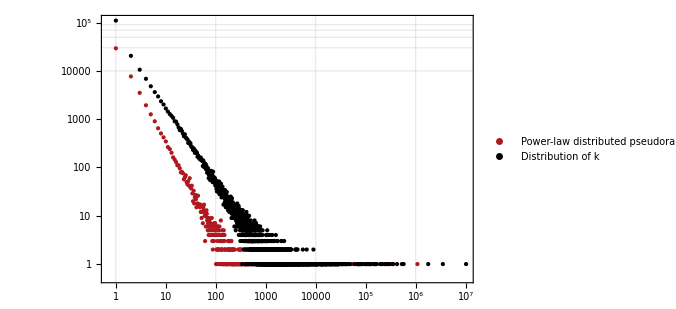

```mathematica
data1 = RandomVariate[ZipfDistribution[0.95],50000];
data2 = Flatten[Table[Diff[Sort[RandomVariate[ZipfDistribution[0.95],200]]],10000]];

HistogramPointPlot[
{data1,data2},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"Power-law distributed pseudorandom numbers l", "Distribution of k"}
]
```

```mathematica
PDF[ZipfDistribution[0.95],l]
```

Piecewise[{{0.590169/l^1.95, l≥1}, {0, True}}]